```mathematica
SimpleTestCase[graph_?GraphQ]:=LinearOptimization[Total[Flatten[WeightedAdjacencyMatrix[Graph[EdgeList[graph,_UndirectedEdge]]].(x+Transpose[x])+WeightedAdjacencyMatrix[Graph[EdgeList[graph,_DirectedEdge]]].(x)],2],{x+Transpose[x]\[VectorGreaterEqual]1},{x∈Matrices[{VertexCount[graph],VertexCount[graph]},Integers]}]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<20>, <54>]] is not implemented.

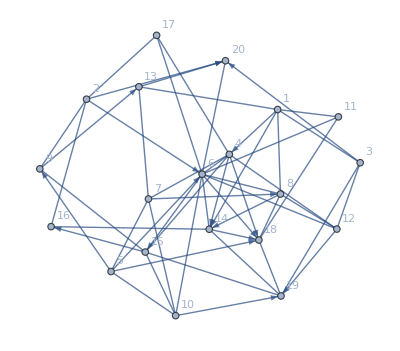
<|Acyclic→False,Bipartite→False,Complete→False,Connected→True,EdgeTransitive→False,WeightedEdge→True,Empty→False,Eulerian→EulerianGraphQ[-Graphics-],Hamiltonian→True,LoopFree→True,Mixed→True,Path→False,Planar→False,Simple→True,Tree→False,Undirected→False,VertexTransitive→False,WeightedVertex→False,WeaklyConnected→True,Weighted→True|>

```mathematica
GraphInformation@randomGraph
```

```mathematica
WeightedAdjacencyMatrix[randomGraph]["ExplicitPositions"]
```

{{1,4},{1,14},{1,3},{1,8},{1,11},{1,13},{2,6},{2,20},{2,9},{2,16},{2,17},{3,20},{3,12},{3,1},{3,19},{4,14},{4,6},{4,18},{4,7},{4,12},{4,15},{4,17},{5,6},{5,9},{5,18},{5,7},{5,10},{6,15},{6,11},{6,8},{6,18},{6,12},{6,10},{6,14},{6,17},{6,20},{7,8},{7,4},{7,5},{7,10},{7,13},{8,14},{8,12},{8,1},{8,18},{9,13},{9,2},{9,15},{10,19},{10,5},{10,6},{10,7},{10,15},{11,1},{11,18},{12,19},{12,4},{13,20},{13,1},{13,7},{14,18},{14,16},{14,6},{14,19},{15,16},{15,4},{15,9},{15,10},{15,19},{16,2},{17,2},{17,4},{17,6},{18,8},{18,11},{18,19},{19,3},{19,14},{19,15},{19,18},{20,6}}

```mathematica
WeightedAdjacencyMatrix[Graph[EdgeList[randomGraph,_UndirectedEdge]]]["ExplicitPositions"]
```

WeightedAdjacencyMatrix[Graph[EdgeList[randomGraph,_UndirectedEdge]]][ExplicitPositions]

```mathematica
EdgeList[randomGraph,_UndirectedEdge]
```

EdgeList[randomGraph,_UndirectedEdge]

```mathematica
ClearAll[SimpleTestCase]
```

```mathematica
SimpleTestCase[graph_?GraphQ]:=LinearOptimization[Total[Flatten[WeightedAdjacencyMatrix[graph].(x+Transpose[x])+WeightedAdjacencyMatrix[graph].(x)],2],{x+Transpose[x]\[VectorGreaterEqual]1},{x∈Matrices[{VertexCount[graph],VertexCount[graph]},Integers]}]
```

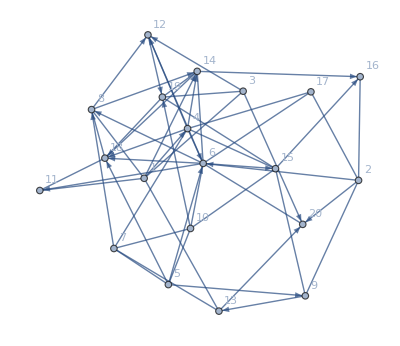

```mathematica
Subgraph[randomGraph,_UndirectedEdge]
```

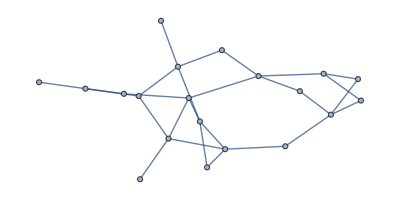

```mathematica
Graph[EdgeList[randomGraph,_UndirectedEdge]]
```

```mathematica
Subgraph[randomGraph,_<->_]
```

-Graphics-

```mathematica
WeightedGraphQ[randomGraph]
```

True

```mathematica
SimpleTestCase[randomGraph]
```

LinearOptimization::ubnd: The problem is unbounded.

{x→{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

```mathematica
LinearOptimization[]
```

```mathematica
LinearOptimization[Flatten[WeightedAdjacencyMatrix[graph]]/2,{x+Transpose[x]\[VectorGreaterEqual]1,},{x∈Matrices[{VertexCount[graph],VertexCount[graph]},Integers]}]
```

```mathematica
LinearOptimization[Flatten[WeightedAdjacencyMatrix[randomGraph]+Transpose[WeightedAdjacencyGraph[randomGraph]]](Flatten[WeightedAdjacencyMatrix[randomGraph]]),constraints,{x∈Matrices[{VertexCount[graph],VertexCount[graph]},Integers]}]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

```mathematica
randomGraph=RandomWeightedMixedGraph[{20,54},0.5,RandomReal[]&,VertexLabels->Automatic]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[randomGraph]//MatrixForm
```

(0. | 0. | 0.694877 | 0.635306 | 0. | 0. | 0. | 0.790414 | 0. | 0. | 0.670291 | 0. | 0.0286234 | 0.986634 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.604842 | 0. | 0. | 0.826107 | 0. | 0. | 0. | 0. | 0. | 0. | 0.763001 | 0.0138135 | 0. | 0. | 0.180967
0.694877 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.18199 | 0. | 0. | 0. | 0. | 0. | 0. | 0.731487 | 0.285921
0. | 0. | 0. | 0. | 0. | 0.59794 | 0.156088 | 0. | 0. | 0. | 0. | 0.528507 | 0. | 0.520474 | 0.0684273 | 0. | 0.906035 | 0.468775 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.954904 | 0.982556 | 0. | 0.277963 | 0.644955 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0254517 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.663758 | 0. | 0.757911 | 0.0239278 | 0.117077 | 0. | 0.251992 | 0.270003 | 0. | 0.799984 | 0.358435 | 0. | 0.619336
0. | 0. | 0. | 0.156088 | 0.982556 | 0. | 0. | 0.364683 | 0. | 0.495964 | 0. | 0. | 0.316172 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.790414 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.328795 | 0. | 0.20073 | 0. | 0. | 0. | 0.312067 | 0. | 0.
0. | 0.826107 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.935897 | 0. | 0.617429 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.644955 | 0.757911 | 0.495964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.913869 | 0. | 0. | 0. | 0.711904 | 0.
0.670291 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.323899 | 0. | 0.
0. | 0. | 0. | 0.528507 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.774108 | 0.
0.0286234 | 0. | 0. | 0. | 0. | 0. | 0.316172 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.676754
0. | 0. | 0. | 0. | 0. | 0.251992 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.143358 | 0. | 0.974036 | 0.880712 | 0.
0. | 0. | 0. | 0.0684273 | 0. | 0. | 0. | 0. | 0.617429 | 0.913869 | 0. | 0. | 0. | 0. | 0. | 0.0384618 | 0. | 0. | 0.0303056 | 0.
0. | 0.763001 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0138135 | 0. | 0.906035 | 0. | 0.799984 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.312067 | 0. | 0. | 0.323899 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.224851 | 0.
0. | 0. | 0.731487 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.880712 | 0.0303056 | 0. | 0. | 0.224851 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.619336 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Select[WeightedAdjacencyMatrix[randomGraph][[i,j]]==WeightedAdjacencyMatrix[randomGraph][[j,i]]!=0]
```

```mathematica
Dimensions[WeightedAdjacencyMatrix[randomGraph]]
```

{20,20}

```mathematica
Table[WeightedAdjacencyMatrix[randomGraph][[i,j]],{i,First[Dimensions[WeightedAdjacencyMatrix[randomGraph]]]},{j,First@Dimensions[WeightedAdjacencyMatrix[randomGraph]]}]
```

{{0.,0.,0.694877,0.635306,0.,0.,0.,0.790414,0.,0.,0.670291,0.,0.0286234,0.986634,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.604842,0.,0.,0.826107,0.,0.,0.,0.,0.,0.,0.763001,0.0138135,0.,0.,0.180967},{0.694877,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.18199,0.,0.,0.,0.,0.,0.,0.731487,0.285921},{0.,0.,0.,0.,0.,0.59794,0.156088,0.,0.,0.,0.,0.528507,0.,0.520474,0.0684273,0.,0.906035,0.468775,0.,0.},{0.,0.,0.,0.,0.,0.954904,0.982556,0.,0.277963,0.644955,0.,0.,0.,0.,0.,0.,0.,0.0254517,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.663758,0.,0.757911,0.0239278,0.117077,0.,0.251992,0.270003,0.,0.799984,0.358435,0.,0.619336},{0.,0.,0.,0.156088,0.982556,0.,0.,0.364683,0.,0.495964,0.,0.,0.316172,0.,0.,0.,0.,0.,0.,0.},{0.790414,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.328795,0.,0.20073,0.,0.,0.,0.312067,0.,0.},{0.,0.826107,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.935897,0.,0.617429,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.644955,0.757911,0.495964,0.,0.,0.,0.,0.,0.,0.,0.913869,0.,0.,0.,0.711904,0.},{0.670291,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.323899,0.,0.},{0.,0.,0.,0.528507,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.774108,0.},{0.0286234,0.,0.,0.,0.,0.,0.316172,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.676754},{0.,0.,0.,0.,0.,0.251992,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.143358,0.,0.974036,0.880712,0.},{0.,0.,0.,0.0684273,0.,0.,0.,0.,0.617429,0.913869,0.,0.,0.,0.,0.,0.0384618,0.,0.,0.0303056,0.},{0.,0.763001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0138135,0.,0.906035,0.,0.799984,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.312067,0.,0.,0.323899,0.,0.,0.,0.,0.,0.,0.,0.224851,0.},{0.,0.,0.731487,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.880712,0.0303056,0.,0.,0.224851,0.,0.},{0.,0.,0.,0.,0.,0.619336,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

## Position

```mathematica
Position[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}}),0]
```

{{1,2},{2,1}}

```mathematica
Position[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}}),3]
```

{{3,1}}

```mathematica
SameQ[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}})[[1,1]],Transpose[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}})][[1,1]]]
```

True

```mathematica
SameQ[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}})[[2,1]],Transpose[({{1, 0, 1}, {0, 2, 4}, {3, 4, 5}})][[1,1]]]
```

```mathematica
UpperTriangularMatrix
```

```mathematica
Flatten[WeightedAdjacencyMatrix[randomGraph]]
```

SparseArray[…]

```mathematica
Array[Indexed[x,{#1,#2}]&,{10,10}]//MatrixForm
```

(x11 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110
x21 | x22 | x23 | x24 | x25 | x26 | x27 | x28 | x29 | x210
x31 | x32 | x33 | x34 | x35 | x36 | x37 | x38 | x39 | x310
x41 | x42 | x43 | x44 | x45 | x46 | x47 | x48 | x49 | x410
x51 | x52 | x53 | x54 | x55 | x56 | x57 | x58 | x59 | x510
x61 | x62 | x63 | x64 | x65 | x66 | x67 | x68 | x69 | x610
x71 | x72 | x73 | x74 | x75 | x76 | x77 | x78 | x79 | x710
x81 | x82 | x83 | x84 | x85 | x86 | x87 | x88 | x89 | x810
x91 | x92 | x93 | x94 | x95 | x96 | x97 | x98 | x99 | x910
x101 | x102 | x103 | x104 | x105 | x106 | x107 | x108 | x109 | x1010)

```mathematica
Transpose[Array[Indexed[x,{#1,#2}]&,{10,10}]]//MatrixForm
```

(x11 | x21 | x31 | x41 | x51 | x61 | x71 | x81 | x91 | x101
x12 | x22 | x32 | x42 | x52 | x62 | x72 | x82 | x92 | x102
x13 | x23 | x33 | x43 | x53 | x63 | x73 | x83 | x93 | x103
x14 | x24 | x34 | x44 | x54 | x64 | x74 | x84 | x94 | x104
x15 | x25 | x35 | x45 | x55 | x65 | x75 | x85 | x95 | x105
x16 | x26 | x36 | x46 | x56 | x66 | x76 | x86 | x96 | x106
x17 | x27 | x37 | x47 | x57 | x67 | x77 | x87 | x97 | x107
x18 | x28 | x38 | x48 | x58 | x68 | x78 | x88 | x98 | x108
x19 | x29 | x39 | x49 | x59 | x69 | x79 | x89 | x99 | x109
x110 | x210 | x310 | x410 | x510 | x610 | x710 | x810 | x910 | x1010)

```mathematica
WeightedAdjacencyMatrix[randomGraph].(x+Transpose[x])
```

SparseArray[…].(x+Transpose[x])

```mathematica
WeightedAdjacencyMatrix[randomGraph].(Array[Indexed[x,{#1,#2}]&,{10,10}]+Transpose[Array[Indexed[x,{#1,#2}]&,{10,10}]])
```

Dot::dotsh: Tensors … and … have incompatible shapes.

SparseArray[…].{{2 x11,x12+x21,x13+x31,x14+x41,x15+x51,x16+x61,x17+x71,x18+x81,x19+x91,x110+x101},{x12+x21,2 x22,x23+x32,x24+x42,x25+x52,x26+x62,x27+x72,x28+x82,x29+x92,x210+x102},{x13+x31,x23+x32,2 x33,x34+x43,x35+x53,x36+x63,x37+x73,x38+x83,x39+x93,x310+x103},{x14+x41,x24+x42,x34+x43,2 x44,x45+x54,x46+x64,x47+x74,x48+x84,x49+x94,x410+x104},{x15+x51,x25+x52,x35+x53,x45+x54,2 x55,x56+x65,x57+x75,x58+x85,x59+x95,x510+x105},{x16+x61,x26+x62,x36+x63,x46+x64,x56+x65,2 x66,x67+x76,x68+x86,x69+x96,x610+x106},{x17+x71,x27+x72,x37+x73,x47+x74,x57+x75,x67+x76,2 x77,x78+x87,x79+x97,x710+x107},{x18+x81,x28+x82,x38+x83,x48+x84,x58+x85,x68+x86,x78+x87,2 x88,x89+x98,x810+x108},{x19+x91,x29+x92,x39+x93,x49+x94,x59+x95,x69+x96,x79+x97,x89+x98,2 x99,x910+x109},{x110+x101,x210+x102,x310+x103,x410+x104,x510+x105,x610+x106,x710+x107,x810+x108,x910+x109,2 x1010}}

```mathematica
WeightedAdjacencyGraph
```